```mathematica
Get[NotebookDirectory[]<>"tzor/tzor.m"]
```

Tzór for Theorized package of sum rules.

Get Lastest Version : [Tzor@github](https://github.com/amapoplar/Tzor)

Author : poplar, xlchen, zzchen, dklian

Version : alpha

Lastest Veresion : This Version

```mathematica
GField[n,x][si[{μ,ν}]]
QFieldB[q,a,α,x]
```

G_μν^n(x)

(q̄)_α^a(x)

```mathematica
wickContract[GField[n,0][si[{μ,ν}]]**QField[q,a1,α1,x]**GField[n,x][si[{μ2,ν}]]**QFieldB[q,a2,α2,0]]
traceContract[%]
```

ⅈ S_α1α2^(q,a1a2)(x) ⟨G_μν^n(0)G_μ2ν^n(x)⟩

ⅈ S_a1a2^q(x) ⟨G_μν^n(0)G_μ2ν^n(x)⟩

```mathematica
jc =((QField[u,a1,α1,x]**M1[si[{α1,β1}]]**QField[d,b1,β1,x])**M2[si[{γ1,δ1}]]**QField[u,c1,δ1,x])**(QFieldB[s,d1,σ1,x]**M2[si[{σ1,ϵ1}]]**QField[s,d1,ϵ1,x])
jcbar = (QFieldB[s,d2,α2,0]**M5[si[{α2,β2}]]**QField[s,d2,β2,0])**(QFieldB[u,c2,γ2,0]**M5[si[{γ2,δ2}]]**(QFieldB[d,b2,σ2,0]**M1[si[{σ2,ϵ2}]]**QFieldB[u,a2,ϵ2,0]))
(*wickContract 函数可以进行Wick收缩*)
wick= wickContract[jc**jcbar]//Expand
(*但一般情形下，我们需要的是不含矩阵指标形式的形式，可以使用traceContract继续计算*)
traceContract[wick[[1]]]+traceContract[wick[[2]]]
```

u_α1^a1(x)**M1_α1β1**d_β1^b1(x)**M2_γ1δ1**u_δ1^c1(x)**(s̄)_σ1^d1(x)**M2_σ1ϵ1**s_ϵ1^d1(x)

(s̄)_α2^d2(0)**M5_α2β2**s_β2^d2(0)**(ū)_γ2^c2(0)**M5_γ2δ2**(d̄)_σ2^b2(0)**M1_σ2ϵ2**(ū)_ϵ2^a2(0)

ⅈ M1_α1β1 M1_σ2ϵ2 M2_γ1δ1 M2_σ1ϵ1 M5_α2β2 M5_γ2δ2 S_α1γ2^(u,a1c2)(x) S_δ1ϵ2^(u,c1a2)(x) S_β1σ2^(d,b1b2)(x) S_ϵ1α2^(s,d1d2)(x) S_β2σ1^(s,d2d1)(-x)-ⅈ M1_α1β1 M1_σ2ϵ2 M2_γ1δ1 M2_σ1ϵ1 M5_α2β2 M5_γ2δ2 S_α1ϵ2^(u,a1a2)(x) S_β1σ2^(d,b1b2)(x) S_δ1γ2^(u,c1c2)(x) S_ϵ1α2^(s,d1d2)(x) S_β2σ1^(s,d2d1)(-x)

ⅈ (tr(S_d1d2^s(x).M5.S_d2d1^s(-x).M2)) M2.S_c1a2^u(x).M1^T.(S_b1b2^d(x))^T.M1^T.S_a1c2^u(x).M5-ⅈ M2.S_c1c2^u(x).M5 (tr(S_d1d2^s(x).M5.S_d2d1^s(-x).M2)) (tr(S_b1b2^d(x).M1.(S_a1a2^u(x))^T.M1))

```mathematica
Trans[a]
```

a^T

```mathematica
NColorFactors[structF[a,b,c]structF[a1,b1,c1]deltaAdj[a,a1]deltaAdj[b,b1]deltaAdj[c,c1]]
```

24

```mathematica
IdentityMatrix[8][[1,2]]
```

0

```mathematica
f =Table[{0,0,0},{8},{8},{8}];
f[[]]=
```

```mathematica
slash[x]
```

x̂

```mathematica
gamma[μ]
```

γ^μ

```mathematica
metric[k,k]
```

D

```mathematica
fourVector[x,μ]
```

x_μ

```mathematica
fourVector[x,μ]fourVector[p,μ]
```

p_μ x_μ

```mathematica
CJM
```

C

```mathematica
Trans[gamma[μ].a.gamma[ν]]
```

(γ^μ.a.γ^ν)^T

```mathematica
factorsp[a,b,q,x,#]&/@Alphabet[][[;;16]]
```

{ⅈ δ^ab 1/(x^2-m_q^2) (m_q+x̂),-1/2 ⅈ g_s G_μ1ν1^η1(0) 1/((x^2-m_q^2)^2) λ_ab^η1 (σ^μ1ν1.(m_q+x̂)+(m_q+x̂).σ^μ1ν1),0,0,0,0,0,0,1/12 ⅈ m_q δ^ab (x̂ m_q+x^2) ⟨g^2 G^2⟩ 1/((x^2-m_q^2)^4),0,0,0,-1/8 ⅈ g_s 1/((x^2-m_q^2)^2) λ_ab^η12 (σ^μ12ν12.(m_q+x̂)+(m_q+x̂).σ^μ12ν12),0,0,0}

```mathematica
factorsp[a,b,q,x,#]&/@Alphabet[][[;;16]]
```

{ⅈ δ^ab 1/(x^2-m_q^2) (m_q+x̂),-1/2 ⅈ g_s G_μ17ν17^η17(0) 1/((x^2-m_q^2)^2) λ_ab^η17 (σ^μ17ν17.(m_q+x̂)+(m_q+x̂).σ^μ17ν17),0,0,0,0,0,0,1/12 ⅈ m_q δ^ab (x̂ m_q+x^2) ⟨g^2 G^2⟩ 1/((x^2-m_q^2)^4),0,0,0,-1/8 ⅈ g_s 1/((x^2-m_q^2)^2) λ_ab^η28 (σ^μ28ν28.(m_q+x̂)+(m_q+x̂).σ^μ28ν28),0,0,0}

```mathematica
Get[NotebookDirectory[]<>"tzor/tzor.m"]
```

Tzór for Theorized package of sum rules.

Get Lastest Version : [Tzor@github](https://github.com/amapoplar/Tzor)

Author : poplar, xlchen, zzchen, dklian

Version : alpha

Lastest Veresion : This Version

```mathematica
Format[eplison4[μ_,ν_,λ_,ρ_],TraditionalForm]:=DisplayForm[SuperscriptBox["ϵ",RowBox[{μ,ν,λ,ρ}]]]
Format[gamma5,TraditionalForm]:=DisplayForm[SuperscriptBox["γ","5"]]
diracContract[a__]:=Module[{gammalist = a,
rPlus = {Dot[f___,b_+c_,l___]:>Dot[f,b,l]+Dot[f,c,l]},rTimes ={Dot[f___,g_gamma b_,l___]:> b Dot[f,g,l],Dot[f___,g_Dot  b_?NumberQ,l___]:> b Dot[f,g,l],Dot[f___,g_Dot  eplison4[b___]n_?NumberQ,l___]:>n eplison4[b] Dot[f,g,l],
Dot[f___,g_Dot  eplison4[b___]n_?NumberQ ,l___]:>n eplison4[b] Dot[f,g,l]},
rIter = {Dot[f___,gamma[μ_].gamma[ν_].gamma[ρ_],l___]:> metric[μ,ν]Dot[f,gamma[ρ],l]+metric[ν,ρ]Dot[f,gamma[μ],l]-metric[μ,ρ]Dot[f,gamma[ν],l]-ⅈ eplison4[indexNew["σ"],μ,ν,ρ]Dot[f,gamma[indexNew["σ","EndQ"->True]],l,gamma5]},
rMetric = {eplison4[___,μ_,___,μ_,___]:> 0,metric[ν_,μ_]metric[μ_,λ_]:>metric[ν,λ],metric[μ_,ν_]^n_:> dim metric[μ,ν]^(n-2),metric[μ_,λ_]gamma[μ_]:> gamma[λ],metric[μ_,λ_] eplison4[l___,μ_,f___]:>eplison4[l,λ,f],metric[μ_,ν_]Dot[f___,gamma[μ_],l___]:>Dot[f,gamma[ν],l]}
},
gammalist = gammalist/.{sigma[μ_,ν_]:> ⅈ metric[μ,ν]- ⅈ gamma[ν].gamma[μ]};

gammalist = Expand[gammalist//.Join[rPlus,rTimes,rIter]];

gammalist =gammalist//.Join[rPlus,rTimes,rMetric];
Print[gammalist];
gammalist = gammalist//.Join[{Dot[f___,gamma5,l___]:>Dot[f,l,gamma5]},rIter];
gammalist/.{Dot[f___,gamma5,gamma5]:> Dot[f],eplison4[lis__]:>Signature[{lis}]eplison4@@Sort[{lis}] }
]
diracContract[gamma[μ].(a gamma[ν]).sigma[λ,ν].gamma[μ]]/.dim->4
```

ⅈ a D^2 γ^λ-2 ⅈ a D γ^λ+a γ^μ.γ^ν.(ⅈ g_λν).γ^μ

a γ^μ.γ^ν.(ⅈ g_λν).γ^μ+8 ⅈ a γ^λ

```mathematica
Det[{{delta[λ,μ],delta[λ,ν],delta[λ,σ],delta[λ,σ2]},{delta[μ,μ],delta[μ,ν],delta[μ,σ],delta[μ,σ2]},
{delta[ν,μ],delta[ν,ν],delta[ν,σ],delta[μ,σ2]},
{delta[σ,μ],delta[σ,ν],delta[σ,σ],delta[σ,σ2]}}]//.{delta[a_,a_]:>1,delta[a_,b_]^n_:> delta[a,b]^(n-2),delta[a_,b_]delta[a_,c_]:>delta[b,c]}
```

0

```mathematica
SetAttributes[delta,Orderless]
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
GA[μ].(a GA[ν]).DiracSigma[GA[λ],GA[ν]].GA[μ]//DiracSimplify//Timing
```

{0.03125,6 ⅈ a (γ̄)^λ}

```mathematica
Attributes[metric]
```

{Orderless}

```mathematica
NumberQ[1/2 ⅈ]
```

True

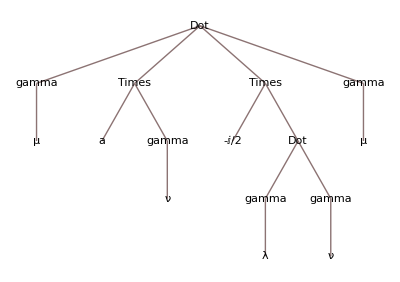

```mathematica
gamma[μ].(a gamma[ν]).(-ⅈ/2 gamma[λ].gamma[ν]).gamma[μ]//TreeForm
```

```mathematica
(*指定悬挂胶子线的图*)
$danglingGluon ={"m","n","o","p"};
(*指定悬挂胶子线的图*)
$quantumPropagators ={"a","b","g","h","i","m","o"};
```

Lell

1/192 ⅈ δ(k1+-p=0) (x^2 δ^ci1ci2 ⟨tzor`Private`gs s̄ σ·Gs⟩).γ^μ.(1/(k1^2) OverHat[k1] δ^ci1ci2)

```mathematica
DE[]
```

```mathematica
factorsx[a,b,q,x,"e"]
```

-(ⅈ x^2 x̂ g_s^2 δ^ab ⟨q̄ q⟩^2)/7776